```mathematica
Quit[]
```

## Tensorial Part

```mathematica
<<xAct`xTensor`
<<xAct`xPert`
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2018, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2018, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$Info=False;
$CVVerbose=False;

SetOptions[ContractMetric,AllowUpperDerivatives->True];
$DefInfoQ=$UndefInfoQ=False;  (*quita las salidas de operaciones*)
$PrePrint=ScreenDollarIndices;
$Pre=ScreenDollarIndices;(* evita que salgan los indices feos *)

$CommuteCovDsOnScalars=True;

DefManifold[M4,4,{a,b,c,d,e,f,g,h,i,j,k,l,m,n,ñ,o,p,q,s,u,v,μ,ν,κ,λ}]

DefMetric[-1,metric[-a,-b],CD,PrintAs->"g"]

Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];

DefMetricPerturbation[metric,metpert,ϵ];
PrintAs[metpert]^="h";

DefTensor[Phi[],M4,PrintAs->"φ"]
DefTensorPerturbation[PertPhi[LI[order]],Phi[],M4,PrintAs->"δφ"]

DefTensor[PhiC[],M4,PrintAs->"φ^*"]
DefTensorPerturbation[PertPhiC[LI[order]],PhiC[],M4,PrintAs->"δφ^*"]
```

We defining X and other constant
Definiendo X=▽_a ϕ ▽^a ϕ^*

```mathematica
DefTensor[X[],M4,PrintAs->"X"]
IndexSet[X[],Scalar[CD[a][Phi[]]CD[-a][PhiC[]]]]

(*DefScalarFunction[V]*)
DefConstantSymbol[ka, PrintAs ->"k"]
DefConstantSymbol[alpha, PrintAs ->"α"]
DefConstantSymbol[eta, PrintAs ->"η"]
DefConstantSymbol[mS, PrintAs ->"m"]
DefConstantSymbol[L1, PrintAs ->"λ_1"]
```

((▽_a φ^*) (▽^a φ))

La definición usada es, arXiv:1404.6495v3
L_2=G_2(ϕ,X)=-λ_1m ϕ^2-α X,
L_3=G_3(ϕ,X)\Box[ϕ]=0, 
G_3=G_5=L_5=0
G_4(ϕ,X) =(k-η/2 X)  
L_4=G_4(ϕ,X) R -2G_(4,X)(ϕ,X)[(\Box(ϕ))^2-ϕ^ab ϕ_ab]+F_4(ϕ,X)(e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c'),
L_4=(k-η/2 X^2)  R+2 η X [(\Box(ϕ))^2-ϕ^ab ϕ_ab]-2η  (e^abc)_d e^(a'b'c' d)ϕ_a ϕ_a' ϕ_(b b') ϕ_(c c')
F_4(ϕ,X)=(2 G_(4,X))/X
\Box(ϕ)=∇_a ∇^a ϕ

```mathematica
L=Sqrt[-Detmetric[]]*(-mS^2*PhiC[]*Phi[]-alpha*X[]+(ka-eta/2*X[]X[])*RicciScalarCD[]+2eta *X[]*(CD[-a]@CD[a]@PhiC[]*CD[-b]@CD[b]@Phi[]-CD[a]@CD[b]@PhiC[]*CD[-a]@CD[-b]@Phi[]))
```

√(-g^OverTilde[~]) (-m^2 φ φ^*-α ((▽_a φ^*) (▽^a φ))+R[▽] (k-1/2 η ((▽_a φ^*) (▽^a φ))^2)+2 η ((▽_a φ^*) (▽^a φ)) (-(▽^a▽^b φ^*) (▽_b▽_a φ)+(▽_a▽^a φ^*) (▽_b▽^b φ)))

```mathematica
Lpert=ToCanonical@NoScalar@ContractMetric@ExpandPerturbation@Perturbation@L;
```

Equation of motion for ϕ, remember i we need divide for 2

```mathematica
Eϕ=(VarD[PertPhi[LI[1]],CD][Lpert]/Sqrt[-Detmetric[]]/.delta[-LI[1],LI[1]]->1)//SeparateMetric[metric]//RicciToEinstein//ContractMetric//ToCanonical//Simplification//Simplify
```

-m^2 φ^*+α (▽_a▽^a φ^*)-2 η (▽_a▽_c▽^c φ^*) (▽^a φ^*) (▽_b▽^b φ)+η R[▽] (▽_a φ^*) (▽^a φ) (▽_b▽^b φ^*)-2 η (▽_a▽_c▽^c φ) (▽^a φ^*) (▽_b▽^b φ^*)+η (▽_a φ^*) (▽^a φ) (▽_b R[▽]) (▽^b φ^*)+η R[▽] (▽^a φ^*) (▽_b▽_a φ) (▽^b φ^*)+η R[▽] (▽^a φ) (▽_b▽_a φ^*) (▽^b φ^*)+4 η (▽^a φ^*) (▽_b▽_c▽^c φ^*) (▽^b▽_a φ)+4 η (▽^a φ) (▽_b▽_c▽^c φ^*) (▽^b▽_a φ^*)-2 η (▽_a φ^*) (▽^a φ) (▽_c▽_b▽^c▽^b φ^*)-2 η (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)+6 η (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)+2 η (▽^a φ^*) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ)+2 η (▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ^*)-4 η (▽^a φ^*) (▽^b▽_a φ) (▽_c▽^c▽_b φ^*)-4 η (▽^a φ) (▽^b▽_a φ^*) (▽_c▽^c▽_b φ^*)+2 η (▽_a φ^*) (▽^a φ) (▽_c▽^c▽_b▽^b φ^*)-4 η (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)+2 η (▽_a▽_c▽_b φ^*) (▽^a φ^*) (▽^c▽^b φ)+2 η (▽_a▽_c▽_b φ) (▽^a φ^*) (▽^c▽^b φ^*)-2 η (▽^a φ^*) (▽_c▽_b▽_a φ) (▽^c▽^b φ^*)-2 η (▽^a φ) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ^*)

```mathematica
ruleflat:={RicciScalarCD[]-> 0,RicciCD[μ_,ν_]-> 0,RiemannCD[μ_,ν_,γ_,θ_]-> 0,Detg[]->-1};
```

```mathematica
Ecuϕ=(ContractMetric[SortCovDs[Eϕ,CD],AllowUpperDerivatives->True]//ReplaceDummies//ToCanonical //Simplification //ContractMetric//Simplify)/.ruleflat
```

-m^2 φ^*+α (▽_a▽^a φ^*)-2 η (▽_a▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c φ^*)+6 η (▽_b▽_a φ^*) (▽^b▽^a φ) (▽_c▽^c φ^*)-2 η (▽^a φ^*) (▽_b▽^b φ) (▽_c▽^c▽_a φ^*)+2 η (▽^a φ) (▽_b▽^b φ^*) (▽_c▽^c▽_a φ^*)-4 η (▽^b▽^a φ) (▽_c▽_b φ^*) (▽^c▽_a φ^*)+2 η (▽^a φ^*) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ)-2 η (▽^a φ) (▽_c▽_b▽_a φ^*) (▽^c▽^b φ^*)

Now let’s use xCoba to set up the coordinate system we want. Let’s use a esferically system. We first define the chart:

```mathematica
DefChart[esf,M4,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Then the metric

```mathematica
MatrixForm[metricarray={{-1,0,0,0},{0,1,0,0},{0,0,r[]^2,0},{0,0,0,r[]^2 Sin[θ[]]^2}}]
```

(-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

Then compute everything we need:

```mathematica
MetricInBasis[metric,-esf,metricarray]
```

{{g |   |  
0 | 0→-1,g |   |  
0 | 1→0,g |   |  
0 | 2→0,g |   |  
0 | 3→0},{g |   |  
1 | 0→0,g |   |  
1 | 1→1,g |   |  
1 | 2→0,g |   |  
1 | 3→0},{g |   |  
2 | 0→0,g |   |  
2 | 1→0,g |   |  
2 | 2→r^2,g |   |  
2 | 3→0},{g |   |  
3 | 0→0,g |   |  
3 | 1→0,g |   |  
3 | 2→0,g |   |  
3 | 3→r^2 Sin[θ]^2}}

```mathematica
MetricCompute[metric,esf,All,CVSimplify->Simplify]
```

### Pasando las ecuaciones a coordenadas

```mathematica
DefScalarFunction[φ,PrintAs->"ϕ"]
DefConstantSymbol[w]
```

Next, we need to set the scalar to be ϕ= φ(r)Exp[-iwt]

```mathematica
ComponentValue[Phi[],φ[r[]]Exp[ⅈ w t[]]]
ComponentValue[PhiC[],φ[r[]]Exp[-ⅈ w t[]]]
```

φ→ⅇ^(ⅈ w t) ϕ[r]

φ^*→ⅇ^(-ⅈ w t) ϕ[r]

```mathematica
?ImplodedTensorValues
```

```mathematica
$CCSimplify=Simplify@ToValues@#&;
ImplodedTensorValues[CD,Phi,esf];
ChangeComponents[CDPhi[a]//ToBasis[esf]//ToValues,CDPhi[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhi,esf];
ChangeComponents[CDCDPhi[a,b]//ToBasis[esf],CDCDPhi[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhi,esf];
ChangeComponents[CDCDCDPhi[a, b,c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];ChangeComponents[CDCDCDPhi[a, b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[a,-b,-c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, b, -c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhi[-a, -b, c]//ToBasis[esf],CDCDCDPhi[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,PhiC,esf];
ChangeComponents[CDPhiC[a]//ToBasis[esf]//ToValues,CDPhiC[-a]//ToBasis[esf]//ToValues];
ImplodedTensorValues[CD,CDPhiC,esf];
ChangeComponents[CDCDPhiC[a,b]//ToBasis[esf],CDCDPhiC[-a,-b]//ToBasis[esf]];
ImplodedTensorValues[CD,CDCDPhiC,esf];
ChangeComponents[CDCDCDPhiC[a, b,c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a, b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[a,-b,-c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, b, -c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];
ChangeComponents[CDCDCDPhiC[-a, -b, c]//ToBasis[esf],CDCDCDPhiC[-a,-b,-c]//ToBasis[esf]];

ImplodedTensorValues[CD,RicciScalarCD,esf];
ChangeComponents[CDRicciScalarCD[a]//ToBasis[esf]//ToValues,CDRicciScalarCD[-a]//ToBasis[esf]//ToValues];

ImplodedTensorValues[CD,RicciCD,esf];
ChangeComponents[CDRicciCD[a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,b,-c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[a,-b,- c]//ToBasis[esf],CDRicciCD[-a, -b,-c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,b, -c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
ChangeComponents[CDRicciCD[-a,-b, c]//ToBasis[esf],CDRicciCD[-a, -b, -c]//ToBasis[esf]];
```

```mathematica
(*
ImplodedTensorValues[CD,CDCDCDPhi,esf];
ChangeComponents[CDCDCDCDPhi[a,b,c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a, b,c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];ChangeComponents[CDCDCDCDPhi[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a,-b,-c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, b, c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, -b, -c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[-a, b, -c,d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhi[a, -b, c,-d]//ToBasis[esf],CDCDCDCDPhi[-a,-b,-c,-d]//ToBasis[esf]];

ImplodedTensorValues[CD,CDCDCDPhiC,esf];
ChangeComponents[CDCDCDCDPhiC[a,b,c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a, b,c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];ChangeComponents[CDCDCDCDPhiC[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a,-b,-c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, b, c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, -b, -c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, -b, c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a, b,-c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[-a, b, -c,d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
ChangeComponents[CDCDCDCDPhiC[a, -b, c,-d]//ToBasis[esf],CDCDCDCDPhiC[-a,-b,-c,-d]//ToBasis[esf]];
*)
```

If we want to see these values, we first need to put it in the appropriate basis, and then ask xCoba to substitute in the appropriate value. Note that you may need to use ToValues multiple times.

```mathematica
Hesϕ=Ecuϕ//Implode//ToBasis[esf]//TraceBasisDummy//ComponentArray//ToValues//ToValues//ToValues//ToValues//ToValues//ToValues//Simplify
```

1/r^2 ⅇ^(-ⅈ w t) (2 α r ϕ'[r]-24 η w^2 r ϕ'[r]^3+α r^2 ϕ''[r]-4 η (3+4 w^2 r^2) ϕ'[r]^2 ϕ''[r]-8 η w^4 r ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-ϕ[r] ((m^2-α w^2) r^2+4 η w^2 (5+2 w^2 r^2) ϕ'[r]^2+40 η w^2 r ϕ'[r] ϕ''[r]))

```mathematica
eqϕ=Collect[Hesϕ* r^2*ⅇ^(ⅈ w t),{alpha,eta}, Simplify]
```

-m^2 r^2 ϕ[r]+α r (w^2 r ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 w^4 r ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 w^2 r^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 w^2 r ϕ'[r]+(3+4 w^2 r^2) ϕ''[r]))

### Solved the System of equation

```mathematica
DDPhi=Solve[eqϕ==0//.{r[]-> r,ka-> k, eta -> η,alpha-> α},{D[D[φ[r],r],r]}][[1,1]]/.Rule->Equal//Simplify
```

ϕ''[r]==(16 r w^4 η ϕ[r]^2 ϕ'[r]-2 r ϕ'[r] (α-12 w^2 η ϕ'[r]^2)+ϕ[r] (r^2 (m^2-w^2 α)+4 w^2 (5+2 r^2 w^2) η ϕ'[r]^2))/(r^2 α-8 r^2 w^4 η ϕ[r]^2-40 r w^2 η ϕ[r] ϕ'[r]-4 (3+4 r^2 w^2) η ϕ'[r]^2)

```mathematica
SDDPhi=eqϕ==0//.{r[]-> r,ka-> k, eta -> η,alpha-> α}
```

-m^2 r^2 ϕ[r]+r α (r w^2 ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 r^2 w^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 r w^2 ϕ'[r]+(3+4 r^2 w^2) ϕ''[r]))==0

Phi’=0

## General solutions

```mathematica
Quit[]
```

```mathematica
eqphi=-m^2 r^2 ϕ[r]+r α (r w^2 ϕ[r]+2 ϕ'[r]+r ϕ''[r])+η (-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 r^2 w^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 r w^2 ϕ'[r]+(3+4 r^2 w^2) ϕ''[r]))==0;
```

### Adim

```mathematica
eqad=eqphi[[1]]/.{w-> ω mS, ϕ[r]-> σ/(mS^2 Sqrt[η]), ϕ'[r]-> dσ/(mS Sqrt[η]),ϕ''[r]->  ddσ/ Sqrt[η]}/.r-> x/mS//Simplify
```

(-24 dσ^3 x ω^2-4 dσ^2 σ ω^2 (5+2 x^2 ω^2)+x^2 σ (-1+α ω^2)+2 dσ x (α-8 σ^2 ω^4)+ddσ (-40 dσ x σ ω^2-4 dσ^2 (3+4 x^2 ω^2)+x^2 (α-8 σ^2 ω^4)))/(mS^2 √η)

```mathematica
eqSol=eqphi[[1]]/.{w-> ω , ϕ[r]-> σ, ϕ'[r]-> dσ,ϕ''[r]->  ddσ}/.r-> x/.{η-> 1, mS-> 1}//Simplify
```

-x^2 σ-8 x (2 dσ+ddσ x) σ^2 ω^4-4 dσ σ ω^2 (10 ddσ x+dσ (5+2 x^2 ω^2))-4 dσ^2 (6 dσ x ω^2+ddσ (3+4 x^2 ω^2))+x α (2 dσ+x (ddσ+σ ω^2))

```mathematica
Simplify[eqad*mS^2 √η]-eqSol//Simplify
```

0

### Serie

```mathematica
seEq=(Series[eqphi[[1]],{r,0,8}]//Simplify)/.φ'[0]-> 0;
ord0=Coefficient[seEq,r,0];
ord1=Coefficient[seEq,r,1];
ord2=Coefficient[seEq,r,2];
ord3=Coefficient[seEq,r,3];
ord4=Coefficient[seEq,r,4];
ord5=Coefficient[seEq,r,5];
ord6=Coefficient[seEq,r,6];
ord7=Coefficient[seEq,r,7];
ord8=Coefficient[seEq,r,8];
```

```mathematica
eqPhi=Series[ϕ[r],{r,0,8}]/.φ'[0]-> 0//Normal;
eqdPhi=Series[ϕ'[r],{r,0,7}]/.φ'[0]-> 0//Normal;
```

```mathematica
(* one *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[1]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond1={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* two *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[2]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond2={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(* three *)
ClearAll[w,mS,η, d2ϕ,d3ϕ,d4ϕ,d5ϕ,d6ϕ,d7ϕ,d8ϕ]
d2ϕ=Last[Assuming[w>0&&mS>0&&φ[0]>0&&η∈Reals, Refine[Solve[ord2==0,φ''[0]]//Simplify]][[3]]];
(*d2ϕ=Last@Solve[ord2==0,φ''[0]];*)
d3ϕ=Last@Solve[ord3==0/.d2ϕ,Derivative[3][φ][0]];
d4ϕ=Last@Solve[ord4==0/.d2ϕ/.d3ϕ,Derivative[4][φ][0]];
d5ϕ=Last@Solve[ord5==0/.d2ϕ/.d3ϕ/.d4ϕ,Derivative[5][φ][0]];
d6ϕ=Last@Solve[ord6==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ,Derivative[6][φ][0]];
d7ϕ=Last@Solve[ord7==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ,Derivative[7][φ][0]];
d8ϕ=Last@Solve[ord8==0/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ,Derivative[8][φ][0]];

cond3={φ[rMin]==eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ, φ'[rMin] ==eqdPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ}/.{φ[0]-> ϕ0, φ'[0]-> 0,r-> rMin};
```

```mathematica
(*sigma=eqPhi/.d2ϕ/.d3ϕ/.d4ϕ/.d5ϕ/.d6ϕ/.d7ϕ/.d8ϕ;*)
```

#### Algorithm

```mathematica
ClearAll[w,mS,η,rMin,ϕ0]
```

```mathematica
SeidelEqsList={};
SeidelBCList1={};
SeidelBCList2={};
SeidelBCList3={};
SeidelCoefFunctionsList={};
AppendTo[SeidelEqsList,{eqphi}];
AppendTo[SeidelCoefFunctionsList,{φ}];

AppendTo[SeidelBCList1,cond1];
AppendTo[SeidelBCList2,cond2];
AppendTo[SeidelBCList3,cond3];

(*AppendTo[SeidelBCList,{φ[rMin]==ϕ0, φ'[rMin] == 0 }];*)
```

```mathematica
ini={SeidelBCList1, SeidelBCList2, SeidelBCList3};
```

### Oscilaciones amortiguadas

```mathematica
L1=1; η=-1;ϕ0=0.05;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.001; w="1.003990881059881000"(*1.005635727502066000*); rMax=1000; α=1;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList1},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

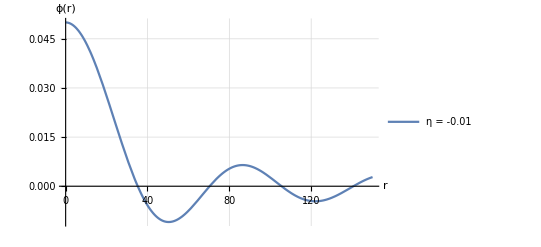

```mathematica
Plot[{Evaluate[φ[r]/.s1]},{r,rMin,150},
Background->White,PlotLegends->Placed[{"η = -0.01"(*, "η = 0.01","η = 0.1"*), "η = -0.05","η = -0.09"(*, "η = -0.01","η = -0.1"*), "η = -0.2","η = -0.05",,"η = -0.05"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->Automatic]
```

```mathematica
L1=1; η=-0.05;ϕ0=0.5;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.001; w="1.002057692316372000"(*1.005635727502066000*); rMax=1000; α=1;
s2=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

#### asintótico

```mathematica
0.5*Sqrt[0.09]
```

0.15

```mathematica
L1=1; η=-1;ϕ0=0.15;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.1; w=1.004787095525063000(*1.005635727502066000*); rMax=100000; α=1;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[{{0.1, 100000.}}, <>]}}

```mathematica
L1=1; η=-0.09;ϕ0=0.5;(* 1.566147319255175890 "1.565204085944661880" *)
k=1/16/ π;mS=1;rMin=0.1; w=1.004787095525063000(*1.005635727502066000*); rMax=100000; α=1;
s1=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[{{0.1, 100000.}}, <>]}}

```mathematica
func[r_]:=(2 c1 Cos[r Sqrt[Abs[1-w^2]]-1.5])/r
```

```mathematica
Evaluate[φ[50]/.s1]
```

{-0.108671}

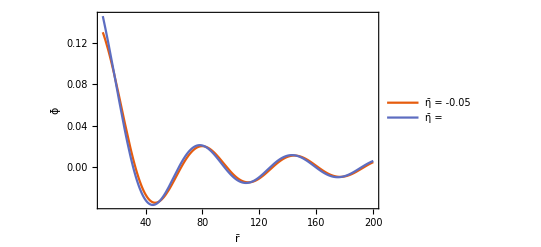

```mathematica
Plot[{Evaluate[φ[r]/.s1],func[r]/.c1->2.8*Sqrt[0.09]},{r,10,200},
Background->White,PlotLegends->Placed[{ "η̄ = -0.05","η̄ = "},{0.75,0.65}],
PlotRange->Full,
GridLines->None,FrameLabel->{"r̄","ϕ̄"},BaseStyle->14,PlotTheme->{"Scientific","Detailed"},PlotStyle->{Automatic,Automatic,{Black,Dashed}}]
```

```mathematica
func2[r_]:=2 c1 Cos[r Sqrt[Abs[1-w^2]]-1.5]
```

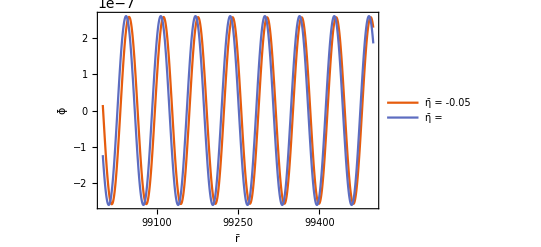

```mathematica
Plot[{Evaluate[φ[r]/.s1],func2[r]/.c1->1.3*10^-7},{r,99000,99500},
Background->White,PlotLegends->Placed[{ "η̄ = -0.05","η̄ = "},{0.75,0.65}],
PlotRange->Full,
GridLines->None,FrameLabel->{"r̄","ϕ̄"},BaseStyle->14,PlotTheme->{"Scientific","Detailed"},PlotStyle->{Automatic,Automatic,{Black,Dashed}}]
```

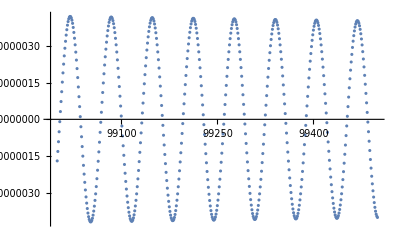

datosXX_Asin_1_p2.dat

```mathematica
datos={};
Do[
AppendTo[datos,{r,Last@Evaluate[φ[r]/.s1]}],{r,99000,99500,1}]
ListPlot[datos,PlotRange->All]
Export["datosXX_Asin_1_p2.dat",datos]
```

```mathematica
LightOrange
```

RGBColor[1, 0.9, 0.8]

### Solitones

#### Shooting

```mathematica
{-1,1.5, 0.568778026578377680,15,0.01,2},{-1,0.75,"0.744851633056108100",15,0.01,2},
```

```mathematica
Amp={0.7};
Dat={};
η=-1;
mS=1;
```

```mathematica
rMin=10^-3;
rMax=15;
UP=0.744851633056108100;(**)
LOW=0.7261983250296968;
```

```mathematica
For[i=1,i<Length[Amp]+1,i++,
ϕ0=Amp[[i]]; 
ϕFlat=0;
rStart=rMin;(*rMin;*)
Clear[newStart];

(* start interval for search of omega, fixed by hand *)
omUP=UP;
omLOW=LOW;

While[ϕFlat==0,

If[newStart==1, 
newStart=0,
ϕFlat=1 ];

For[rTest =rStart+0.03(*rStart*), rTest <rMax+0.03,rTest+=0.1,
(*Print[rTest];*)
If[newStart==1,Break[]]; (* reiniciando rStart con el nuevo valor donde explotó *)

(*Print["rTest= ", rTest];*)
stop=0;

While[stop==0,

Which[ MemoryInUse[] > 5*10^19, (* Controlando la memoria *)
Speak["Mem Oree Full Lee Occupied"];
Print["Memory Full! \n"];ϕFlat=1;Break[],
SetPrecision[(omUP-omLOW)/2,prec]<10^-prec, (* Fijando la maxima precision *)
Speak["Maximum Precision Reached"];
Print["Max.Precision Reched! \n"];ϕFlat=1;Abort[]
           ];

w=(omLOW+omUP)/2;

(*Print[w];*)

s=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rTest+1},Method->{"EquationSimplification"->"Residual"}];

stop=1;

Do[
Which[Evaluate[φ[rp]/.s][[1]]>2ϕ0||Evaluate[φ[rp]/.s][[1]]>Evaluate[φ[rp-0.01]/.s][[1]],
stop=0;
Print["Pos"];
omLOW=w;
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[] (* Sale del ciclo Do *),
Evaluate[φ[rp]/.s][[1]]<-2ϕ0||Evaluate[φ[rp]/.s][[1]]<0,
stop=0;
Print["Neg"];
omUP=w;
rStart=rp;
If[rStart<rTest-0.02,Print["Reiniciando en = ", rStart, " Old = ", rTest];stop=1; newStart=1] (* Saliendo del ciclo While si, el rStart es menor que el rTest *);
Break[](* Sale del ciclo Do *)
](* End Which*),{rp,rMin+0.03,rTest}
](* End Do *)
](* End While *)
 ](* End For that change the rTest value *)
];(* End While ϕFlat==0 *)
Print["Encontrado"];
Print[w];
AppendTo[Dat,{η,ϕ0,w,rTest,rMin,2}];
](* End For that choose the ϕ0 value *);
```

```mathematica
datNViable={};
```

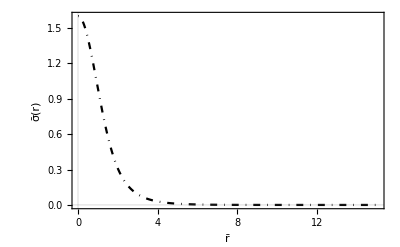

```mathematica
Plot[{Evaluate[φ[x]/.s]},{x,rMin,rTest},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black},AxesOrigin->{0,0}]
```

```mathematica
L1=1; η=1.0;ϕ0=2.96; mS=1;rMin=0.001; w=.961; rMax=20; α=1;(* .26,1.012476348812271000 *)
s=NDSolve[{SeidelEqsList[[1]],ini[[1]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

{{φ→InterpolatingFunction[…]}}

```mathematica
{-1.,3.3,0.42257696476282125,15.060999999999996,30.,0.001,2.}
```

```mathematica
{-1,3.4,.41793856334,20,0.01,2}
```

```mathematica
L1=1; η=-1;ϕ0=3.4; mS=1;rMin=0.001; w=.41793856334; rMax=13; α=1;(* .26,1.012476348812271000 *)
s=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}]
```

NDSolve::ndsz: At r == 1.32628, step size is effectively zero; singularity or stiff system suspected.

{{φ→InterpolatingFunction[…]}}

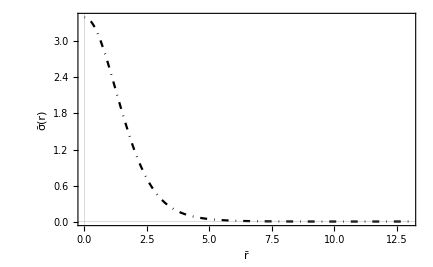

```mathematica
Plot[{Evaluate[φ[x]/.s]},{x,rMin,rMax},
Background->White,
PlotRange->Full,FrameLabel->{"r̄","σ̄(r)"},BaseStyle->14,PlotTheme->{"Scientific"},PlotStyle->{Blue,DotDashed,Black}]
```

#### Test

```mathematica
datViableN[[36]]
```

{-1.,0.42,0.934121,20.061,0.001,2.}

```mathematica
(*σ0, w, rMax, η*)
datViableN={{0.606,0.9999995207157898,201.0000000005957,-1},{0.63,0.9918107720880629,48.35399999997801,-1},{0.66,0.9773564575675739,53.314999999966446,-1},{0.67,0.9723871014804728,47.191999999980716,-1},{0.69,0.9624652220917436,54.62899999996338,-1},{0.7,0.9575473875684575,45.71899999998415,-1},{0.72,0.9478481489709842,26.170000000009,-1},{0.74,0.9383659516701663,33.16000000001342,-1},{0.76,0.9291239932949891,30.983000000014883,-1},{0.78,0.9201313108001683,30,-1},{0.8,0.9113897089244307,19.957000000001408,-1},{0.82,0.9028971062183845,21.124000000002834,-1},{0.84,0.8946481144672654,19.14000000000041,-1},{0.86,0.8866353439752958,18.500999999999628,-1},{0.88,0.878852101130706,28.34600000001166,-1},{0.9,0.8712895259625596,15.53399999999683,-1},{0.92,0.8639400693060306,18.179999999999236,-1},{0.94,0.8567948948772361,14.841999999997213,-1},{0.96,0.8498465804823888,16.706999999997436,-1},{0.98,0.8430871226575917,21.706000000003545,-1},{0.99,0.8397756686359639,17.550999999998467,-1},{1.,0.8365083431232883,17.74999999999871,-1},{1.2,0.7792281406244599,19.28900000000059,-1},{1.4,0.7338129340118398,20.05800000000153,-1},{1.6,0.696688024813614,13.304999999998065,-1},{1.8,0.6655979441170108,19.237000000000528,-1},{2.,0.6390553518425344,17.34199999999821,-1},{2.2,0.6160385486514806,14.640999999997325,-1},{2.4,0.5958204645637497,13.989999999997686,-1},{2.6,0.5778682884855366,10.475999999999633,-1},{2.8,0.5617811490863667,14.050999999997652,-1},{3.,0.5472513804946141,12.197999999998679,-1},{3.2,0.5340384133417744,13.159999999998146,-1},{3.4,0.5219506559272629,13.640999999997879,-1},{3.6,0.5108335204507295,11.065999999999306,-1},{3.8,0.5005611251183273,15.902999999996625,-1},{4.,0.4910292284122836,14.39799999999746,-1},{4.2,0.4821508284497754,10.745999999999484,-1},{4.4,0.4738526759966446,10.48199999999963,-1},{4.6,0.4660726898167017,17.55299999999847,-1},{4.8,0.45875779679090745,15.751999999996709,-1},{5.,0.4518622255255901,11.270999999999193,-1},{5.2,0.44534626650868525,11.481999999999076,-1},{5.4,0.4391754793410385,14.8649999999972,-1},{5.6,0.4333195263659412,14.1459999999976,-1},{5.8,0.42775183524014715,10.42599999999966,-1},{6,0.4224487319929132,10.894999999999401,-1},{6.2,0.41738942075742513,9.821999999999996,-1},{6.4,0.41255518759458343,12.625999999998442,-1},{6.6,0.4079293352782265,13.80099999999779,-1},{6.8,0.40349678011570467,15.359999999996926,-1},{7.,0.3992441870875326,12.622999999998443,-1},{7.2,0.3951591624249573,9.18400000000035,-1},{7.4,0.3912307662288609,12.91599999999828,-1},{7.6,0.38744884712284566,12.830999999998328,-1},{7.8,0.383804326062093,15.015999999997117,-1},{8.,0.38028867151359635,12.040999999998766,-1},{8.2,0.37689437454125085,12.197999999998679,-1},{8.4,0.37361427153800764,11.537999999999045,-1},{8.6,0.37044194713234824,9.889999999999958,-1},{8.8,0.3673713917031838,13.740999999997824,-1},{9,0.3643971614513011,14.799999999997237,-1},{9.2,0.3615140982921379,15.589999999996799,-1},{9.4,0.3587175201595687,11.735999999998935,-1},{9.6,0.35600301426608094,12.018999999998778,-1},{9.8,0.3533665013350388,14.039999999997658,-1},{10,0.3508041927445462,15.070999999997087,-1},{10.5,0.34470048721513374,12.435999999998547,-1},{11,0.33898990027055714,13.505999999997954,-1},{11.5,0.33363061831463847,14.526999999997388,-1},{12,0.3285868089031246,10.667999999999527,-1},{12.5,0.3238277198709476,13.715999999997837,-1},{13,0.31932661731185163,13.473999999997972,-1},{13.5,0.31506018683638926,15.639999999996771,-1},{14,0.3110080394430057,12.945999999998264,-1},{14.5,0.30715221231419754,12.21399999999867,-1},{15,0.3034767278946062,14.353999999997484,-1},{16,0.2966119177794746,11.759999999998922,-1},{17,0.2903176139688094,12.93499999999827,-1},{18,0.28451620983348436,15.037999999997105,-1},{19,0.2791444860990656,10.474999999999634,-1},{20,0.27414997514444917,10.295999999999733,-1},{25,0.2535202002185575,15.091999999997075,-1},{30,0.23790498835005225,15.385999999996912,-1},{35,0.22550549456370222,14.997999999997127,-1},{40,0.21532089827225892,16.621999999997332,-1},{45,0.20674252867311854,17.894999999998888,-1},{100,0.1572902583578016,17.81599999999879,-1},{200,0.12435372586010171,20.75300000000238,-1},{500,0.09134058144401483,25.52200000000821,-1},{600,0.08591815964638728,30,-1},{1000,0.07239699294378885,30.231000000013964,-1},{2000,0.0574112394001,43,-1}};;
```

```mathematica
datViableP={{0.67,0.99998046875,201.0000000005957,1}(*,{0.671,0.9999775303335917,201.00999999996216,1}*),{0.672,0.9999775303335917,201.00999999996216,1},{0.673,0.9999687150843667,201.00999999996216,1},{0.674,0.9999789995417958,201.00999999996216,1},{0.675,0.9999687150843667,201.00999999996216,1},{0.676,0.9999452077531001,201.00999999996216,1},{0.677,0.9999217004218335,201.00999999996216,1},{0.678,0.9998993352826282,142.99000000001493,1},{0.679,0.9998599936772586,201.00999999996216,1},{0.6795,0.9998464261591169,154.76000000000423,1},{0.7,0.9984759995489378,139.73100000030314,1},{0.72,0.9962075834622321,59.9839999999509,1},{0.74,0.9932927009293323,101.01000000011825,1},{0.76,0.9898964354584507,61.42399999994755,1},{0.78,0.9861317754171623,36.83300000000486,1},{0.8,0.9820802824199164,45.97499999998355,1},{0.82,0.9778025103732645,37.79500000000262,1},{0.84,0.9733433353477622,40.168999999997084,1},{0.86,0.9687350122072801,33.8110000000119,1},{0.88,0.9639970167958337,29.653000000013257,1},{0.9,0.9591309602305742,30.142000000013855,1},{0.92,0.95405,20,1}};
```

```mathematica
L1=1; η=1.0;ϕ0=0.9; mS=1;rMin=0.001; w=0.9591309602305742; rMax=30; α=1;(* .26,1.012476348812271000 *)
s1=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];

L1=1; η=1.0;ϕ0=0.92; mS=1;rMin=0.001; w=0.95405; rMax=20; α=1;(* .26,1.012476348812271000 *)
s2=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];
```

```mathematica
{10,0.3508041927445462,15.070999999997087,-1}
```

```mathematica
L1=1; η=-1.0;ϕ0=10; mS=1;rMin=0.001; w=0.3508041927445462; rMax=15.07; α=1;(* .26,1.012476348812271000 *)
s3=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];
```

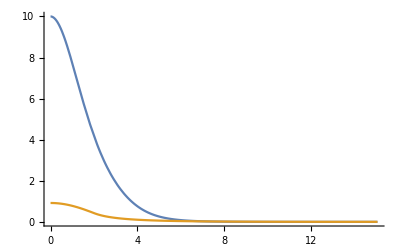

```mathematica
Plot[{Evaluate[φ[r]]/.s3, Evaluate[φ[r]]/.s2},{r,rMin,rMax},PlotRange->All]
```

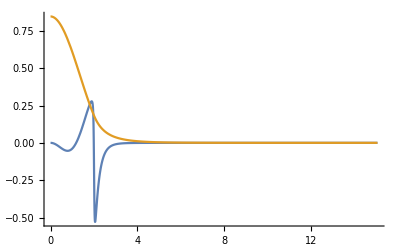

```mathematica
Plot[{Evaluate[(-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 r^2 w^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 r w^2 ϕ'[r]+(3+4 r^2 w^2) ϕ''[r]))]/.s2,Evaluate[ϕ[r]^2]/.s2},{r,rMin,rMax},PlotRange->All]
```

```mathematica
dat={};
Do[AppendTo[dat,{(Evaluate[ϕ[r]]/.s3)[[1]],(Evaluate[m^2 r^2 ϕ[r]-(-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 r^2 w^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 r w^2 ϕ'[r]+(3+4 r^2 w^2) ϕ''[r]))]/.s3)[[1]]}],{r,rMin,rMax,0.01}
]
```

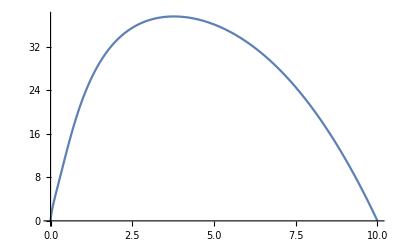

```mathematica
ListPlot[dat,Joined->True,PlotRange->All]
```

```mathematica
-m^2 r^2 ϕ[r]+r α (r w^2 ϕ[r])
```

```mathematica
dat={};
Do[AppendTo[dat,{(Evaluate[ϕ[r]]/.s1)[[1]],(Evaluate[m^2 r^2 ϕ[r]+(+8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 r^2 w^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 r w^2 ϕ'[r]+(3+4 r^2 w^2) ϕ''[r]))]/.s1)[[1]]}],{r,rMin,rMax,0.01}
]
```

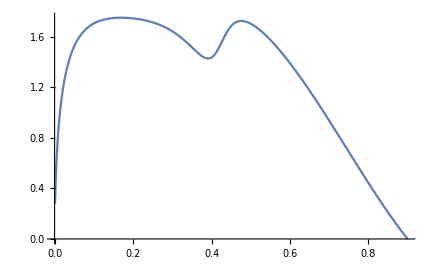

```mathematica
ListPlot[dat,Joined->True,PlotRange->All]
```

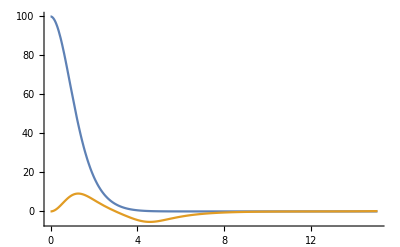

```mathematica
Plot[{Evaluate[ϕ[r]^2]/.s3,Evaluate[-m^2 r^2 ϕ[r]+r α (r w^2 ϕ[r])-(-8 r w^4 ϕ[r]^2 (2 ϕ'[r]+r ϕ''[r])-4 w^2 ϕ[r] ϕ'[r] ((5+2 r^2 w^2) ϕ'[r]+10 r ϕ''[r])-4 ϕ'[r]^2 (6 r w^2 ϕ'[r]+(3+4 r^2 w^2) ϕ''[r]))]/.s3},{r,rMin,rMax},PlotRange->All]
```

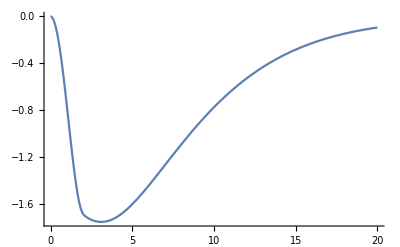

```mathematica
Plot[Evaluate[-m^2 r^2 ϕ[r]]/.s1,{r,rMin,rMax},PlotRange->All]
```

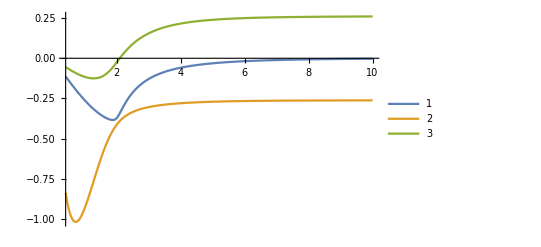

```mathematica
Plot[{Evaluate[φ'[r]]/.s1,Evaluate[-(10 r w^2  φ[r]+√(r^2 (3+76 w^4  φ[r]^2+r^2 (4 w^2-32 w^6  φ[r]^2))))/(6+8 r^2 w^2)]/.s1,Evaluate[(-10 r w^2  φ[r]+√(r^2 (3+76 w^4  φ[r]^2+r^2 (4 w^2-32 w^6  φ[r]^2))))/(6+8 r^2 w^2)]/.s1},{r,0.4,10},PlotLegends->Automatic]
```

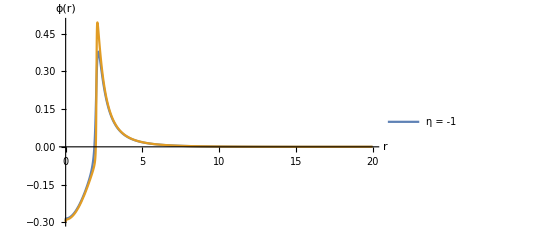

```mathematica
Plot[{Evaluate[φ''[r]/.s1],Evaluate[φ''[r]/.s2](*,Evaluate[φ[r]/.s1]*)},{r,rMin,rMax},
Background->White,PlotLegends->Placed[{"η = -1"},{0.85,0.65}],
PlotRange->Full,AxesLabel->{"r","ϕ(r)"},
GridLines->None]
```

```mathematica
datMa={};
datMe={};
Do[
AppendTo[datMa,{r,(Evaluate[φ''[r]]/.s2)[[1]] }];
AppendTo[datMe,{r,(Evaluate[φ''[r]]/.s1)[[1]] }],
{r,rMin,rMax,0.01}
]
```

```mathematica
Export["XX_P_ProfH_ddMay.dat",datMa]
Export["XX_P_ProfH_ddMen.dat",datMe]
```

XX_P_ProfH_ddMay.dat

XX_P_ProfH_ddMen.dat

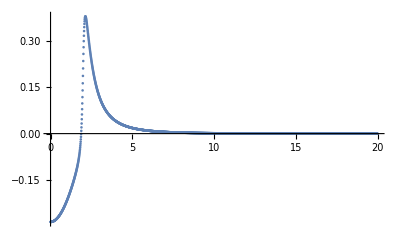

```mathematica
ListPlot[datMe,PlotRange->All]
```

```mathematica
dat={};
dat2={};
Do[AppendTo[dat,{datViableP[[i,2]],datViableP[[i,1]]}];
AppendTo[dat2,datViableP[[i,1]]],{i,1,Length[datViableP]}]
```

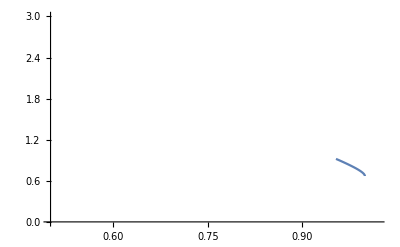

```mathematica
ListPlot[{dat},Joined->True,PlotRange->{{0.5,1.02},{0,3}}]
```

```mathematica
Export["XX_P_solH.dat",dat]
```

XX_P_solH.dat

```mathematica
Table[
AA=minϕ0critBHplus[[i]];
L1=1;
η=AA[[1]];(* cambiar*)
ϕ0=AA[[2]]; 
α=1;
k=1/16/ π;mS=1;rMin=10^-3; rMax=25;
w=0.996540169109419000;

s=NDSolve[{SeidelEqsList[[1]],SeidelBCList[[1]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax},Method->{"EquationSimplification"->"Residual"}];

Plot[{Evaluate[φ[r]/.s]},{r,rMin,rMax},
Background->White,PlotLegends->{Evaluate[φ[rMax]/.s]},
PlotRange->All,AxesOrigin->{0,0},
PlotStyle->{RGBColor[0,0.5,0],Dashing[{0.03,0.015}],Thickness[0.007]},
GridLines->Automatic],{i,1,Length[minϕ0critBHplus]}]
```

```mathematica
{0.9,0.8712895259625596,15.53399999999683,-1},
```

```mathematica
{0.9,0.9591309602305742,30.142000000013855,1}
```

```mathematica
L1=1; η=1.0;ϕ0=0.9; mS=1;rMin=0.001; w=0.9591309602305742; rMax=30; α=1;(* .26,1.012476348812271000 *)
s1=NDSolve[{SeidelEqsList[[1]],ini[[3]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];

L1=1; η=-1.0;ϕ0=0.9; mS=1;rMin=0.001; w=0.8712895259625596; rMax=15; α=1;(* .26,1.012476348812271000 *)
s2=NDSolve[{SeidelEqsList[[1]],ini[[2]]//Chop},SeidelCoefFunctionsList[[1]],{r,rMin,rMax}];
```

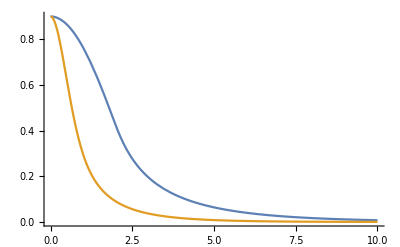

```mathematica
Plot[{Evaluate[φ[r]]/.s1, Evaluate[φ[r]]/.s2},{r,rMin,10},PlotRange->All]
```

```mathematica
datN={};
datP={};
Do[
AppendTo[datN,{r,(Evaluate[φ[r]]/.s2)[[1]] }];
AppendTo[datP,{r,(Evaluate[φ[r]]/.s1)[[1]] }],
{r,rMin,rMax,0.01}
]
```

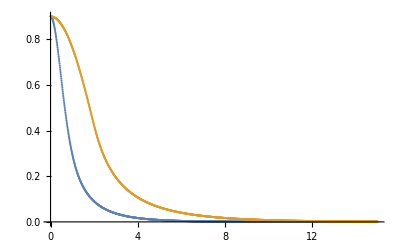

```mathematica
ListPlot[{datN,datP},PlotRange->All]
```

```mathematica
Export["XX_P_ProfH.dat",datP]
Export["XX_N_ProfH.dat",datN]
```

XX_P_ProfH.dat

XX_N_ProfH.dat